```mathematica
ClearAll["Global`*"]
```

# Coupled Qutrit-Qubit Quantum Thermal Diode

In this paper, we propose a quantum thermal diode model based on a coupled qutrit - qubit system to regulate the heat flow between two thermal baths. This numerical simulations show the diode characteristics of our model.  We acknowledge the use of modules and functions of supplementary materials of Ref[31].

#### Pauli Matrices for Two-Level-System (Qubit)

```mathematica
Subscript[σ, x] = ({{0, 1}, {1, 0}}) ;
Subscript[σ, y] = ({{0, -ⅈ}, {ⅈ, 0}});
Subscript[σ, z] = ({{1, 0}, {0, -1}});
Subscript[σ, I] = ({{1, 0}, {0, 1}});
SubPlus[σ] = MatrixForm[1/2*(Subscript[σ, x] + ⅈ*Subscript[σ, y])];
SubMinus[σ] =MatrixForm[1/2*(Subscript[σ, x] - ⅈ*Subscript[σ, y])];
```

There are two energy states in a qubit and they can be described by two column vectors.

```mathematica
Subscript[z, 0]=Transpose[{{0,1}}];
Subscript[z, 1]=Transpose[{{1,0}}];
```

#### Pauli Matrix Equivalents for Three-Level-System (Qutrit)

```mathematica
Subscript[Σ, x] = ({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}) ;
Subscript[Σ, y] = ({{0, -i, 0}, {i, 0, -i}, {0, i, 0}});
Subscript[Σ, z] =({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
Subscript[Σ, I] = ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

There are three energy states in a qutrit and they can be described by three column vectors .

```mathematica
Subscript[Z, 0]=Transpose[{{0,0,1}}];
Subscript[Z, 1]=Transpose[{{0,1,0}}];
Subscript[Z, 2]=Transpose[{{1,0,0}}];
```

#### Qubit Hamiltonian ( assuming ground state energy is 0 and excited state energy is E_3 )

```mathematica
Subscript[H, Two]=Subscript[𝔼, 3]* Subscript[z, 1].Subscript[z, 1] ᵀ;
MatrixForm[%]
```

(𝔼_3 | 0
0 | 0)

#### Qutrit Hamiltonian ( assuming ground state energy is 0 and excited states energies are E_1 and E_2 )

```mathematica
Subscript[H, Three]=Subscript[𝔼, 1]* Subscript[Z, 1].Subscript[Z, 1] ᵀ + Subscript[𝔼, 2]* Subscript[Z, 2].Subscript[Z, 2] ᵀ;
MatrixForm[%]
```

(𝔼_2 | 0 | 0
0 | 𝔼_1 | 0
0 | 0 | 0)

#### Free Hamiltonian of the system

```mathematica
Subscript[H, 0]=KroneckerProduct[Subscript[H, Three],Subscript[σ, I]]+KroneckerProduct[Subscript[Σ, I],Subscript[H, Two]];
MatrixForm[%]
```

(𝔼_2+𝔼_3 | 0 | 0 | 0 | 0 | 0
0 | 𝔼_2 | 0 | 0 | 0 | 0
0 | 0 | 𝔼_1+𝔼_3 | 0 | 0 | 0
0 | 0 | 0 | 𝔼_1 | 0 | 0
0 | 0 | 0 | 0 | 𝔼_3 | 0
0 | 0 | 0 | 0 | 0 | 0)

#### Free Hamiltonian Eigenvalues and Eigenstates

```mathematica
Eigensystem[Subscript[H, 0]]//MatrixForm
```

(0 | 𝔼_1 | 𝔼_2 | 𝔼_3 | 𝔼_1+𝔼_3 | 𝔼_2+𝔼_3
{0,0,0,0,0,1} | {0,0,0,1,0,0} | {0,1,0,0,0,0} | {0,0,0,0,1,0} | {0,0,1,0,0,0} | {1,0,0,0,0,0})

To enable transitions between different states without an input of external energy,we take E_2=E_1+ E_3 (resonance condition). With this condition we now have two degenerate energy eigenstates |11⟩  and |20⟩, which can be swapped without an input from external sources.

|11⟩ State:

```mathematica
KroneckerProduct[Subscript[Z, 1],Subscript[z, 1]]
```

{{0},{0},{1},{0},{0},{0}}

| 20⟩ State:

```mathematica
KroneckerProduct[Subscript[Z, 2],Subscript[z, 0]]
```

{{0},{1},{0},{0},{0},{0}}

Write |11⟩  and |20⟩ states as column vectors:

```mathematica
Subscript[S, 11]=Transpose[{{0,0,1,0,0,0}}];
Subscript[S, 20]=Transpose[{{0,1,0,0,0,0}}];
```

#### Interaction Hamiltonian between qubit and qutrit

For transitions between |11⟩  and |20⟩ , we introduce an interaction Hamiltonian. g is the interaction energy between the qutrit and qubit.

```mathematica
Subscript[H, int]=g *( KroneckerProduct[Subscript[S, 11],Subscript[S, 20] ᵀ]+KroneckerProduct[Subscript[S, 20],Subscript[S, 11] ᵀ]);
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | g | 0 | 0 | 0
0 | g | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

#### Total System Hamiltonian

```mathematica
Subscript[H, s]=Subscript[H, 0]+Subscript[H, int]/.{Subscript[𝔼, 1]+Subscript[𝔼, 3]->Subscript[𝔼, 2]};
MatrixForm[%]
```

(𝔼_2+𝔼_3 | 0 | 0 | 0 | 0 | 0
0 | 𝔼_2 | g | 0 | 0 | 0
0 | g | 𝔼_2 | 0 | 0 | 0
0 | 0 | 0 | 𝔼_1 | 0 | 0
0 | 0 | 0 | 0 | 𝔼_3 | 0
0 | 0 | 0 | 0 | 0 | 0)

As total system Hamiltonian is not diagonalized, we should 1st find it's eigenvalues and eigenvectors in order to find the invertible matrix A ( here the unitary transformation) which creates a diagonalized system Hamiltonian.

```mathematica
{Φ,v}=Eigensystem[Subscript[H, s]]
```

{{0,𝔼_1,-g+𝔼_2,g+𝔼_2,𝔼_3,𝔼_2+𝔼_3},{{0,0,0,0,0,1},{0,0,0,1,0,0},{0,-1,1,0,0,0},{0,1,1,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}}

```mathematica
Norm/@v
```

{1,1,√2,√2,1,1}

#### Eigenstates as the tensor product of individual states

Normalized Eigenstates in matrix form

```mathematica
Subscript[λ, 1]=Transpose[{{1,0,0,0,0,0}}];
Subscript[λ, 2]=Transpose[{{0,1/(√2),1/(√2),0,0,0}}];
Subscript[λ, 3]=Transpose[{{0,-1/(√2),1/(√2),0,0,0}}];
Subscript[λ, 4]=Transpose[{{0,0,0,1,0,0}}];
Subscript[λ, 5]=Transpose[{{0,0,0,0,1,0}}];
Subscript[λ, 6]=Transpose[{{0,0,0,0,0,1}}];
```

A can be formed by having these basis vectors (eigenstates)  as columns.
A=(1 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | -1/(√2) | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
A={{1,0,0,0,0,0},{0,1/(√2),-1/(√2),0,0,0},{0,1/(√2),1/(√2),0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};
```

Then, the diagonalized total system Hamiltonian is,

```mathematica
Subscript[H, sys]=Simplify[Inverse[A].Subscript[H, s].A];
MatrixForm[%]
```

(𝔼_2+𝔼_3 | 0 | 0 | 0 | 0 | 0
0 | g+𝔼_2 | 0 | 0 | 0 | 0
0 | 0 | -g+𝔼_2 | 0 | 0 | 0
0 | 0 | 0 | 𝔼_1 | 0 | 0
0 | 0 | 0 | 0 | 𝔼_3 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[Eigensystem[Subscript[H, sys]]]
```

{{0,𝔼_1,-g+𝔼_2,g+𝔼_2,𝔼_3,𝔼_2+𝔼_3},{{0,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,0,0,0,0,0}}}

Eigenvalues in matrix form

```mathematica
HsEVal ={Subscript[𝔼, 2]+Subscript[𝔼, 3],g+Subscript[𝔼, 2],-g+Subscript[𝔼, 2],Subscript[𝔼, 1],Subscript[𝔼, 3],0}//MatrixForm;
```

New eigenstates in matrix form

```mathematica
Subscript[λ, 1]=Transpose[{{1,0,0,0,0,0}}];
Subscript[λ, 2]=Transpose[{{0,1,0,0,0,0}}];
Subscript[λ, 3]=Transpose[{{0,0,1,0,0,0}}];
Subscript[λ, 4]=Transpose[{{0,0,0,1,0,0}}];
Subscript[λ, 5]=Transpose[{{0,0,0,0,1,0}}];
Subscript[λ, 6]=Transpose[{{0,0,0,0,0,1}}];
```

We can obtain the same eigenstates by taking the tensor product between individual system states.

```mathematica
Subscript[S, i_,j_]:=KroneckerProduct[Subscript[Z, i],Subscript[z, j]]
```

```mathematica
Subscript[S, 2,1]
Subscript[S, 2,0]
Subscript[S, 1,1]
Subscript[S, 1,0]
Subscript[S, 0,1]
Subscript[S, 0,0]
```

{{1},{0},{0},{0},{0},{0}}

{{0},{1},{0},{0},{0},{0}}

{{0},{0},{1},{0},{0},{0}}

{{0},{0},{0},{1},{0},{0}}

{{0},{0},{0},{0},{1},{0}}

{{0},{0},{0},{0},{0},{1}}

## Quantum Master Equation

#### Density Matrix

```mathematica
ρMatrix[t]=Table[Subscript[ρ, i,j][t],{i,1,6},{j,1,6}];
MatrixForm[%]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t] | ρ_(1,5)[t] | ρ_(1,6)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t] | ρ_(2,5)[t] | ρ_(2,6)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t] | ρ_(3,5)[t] | ρ_(3,6)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t] | ρ_(4,5)[t] | ρ_(4,6)[t]
ρ_(5,1)[t] | ρ_(5,2)[t] | ρ_(5,3)[t] | ρ_(5,4)[t] | ρ_(5,5)[t] | ρ_(5,6)[t]
ρ_(6,1)[t] | ρ_(6,2)[t] | ρ_(6,3)[t] | ρ_(6,4)[t] | ρ_(6,5)[t] | ρ_(6,6)[t])

#### Possible Transition Frequencies

```mathematica
ωMatrix={Flatten[Table[Subscript[ω, i,j],{i,1,6},{j,i+1,6}]]}
```

{{ω_(1,2),ω_(1,3),ω_(1,4),ω_(1,5),ω_(1,6),ω_(2,3),ω_(2,4),ω_(2,5),ω_(2,6),ω_(3,4),ω_(3,5),ω_(3,6),ω_(4,5),ω_(4,6),ω_(5,6)}}

```mathematica
ωVals=Flatten[Simplify[Table[(HsEVal[[1,i]]-HsEVal[[1,j]])/ℏ,{i,1,6},{j,i+1,6}]]]/.{Subscript[𝔼, 1]+Subscript[𝔼, 3]->Subscript[𝔼, 2]}
```

{(-g+𝔼_3)/ℏ,(g+𝔼_3)/ℏ,(-𝔼_1+𝔼_2+𝔼_3)/ℏ,𝔼_2/ℏ,(𝔼_2+𝔼_3)/ℏ,(2 g)/ℏ,(g-𝔼_1+𝔼_2)/ℏ,(g+𝔼_2-𝔼_3)/ℏ,(g+𝔼_2)/ℏ,-(g+𝔼_1-𝔼_2)/ℏ,-(g-𝔼_2+𝔼_3)/ℏ,(-g+𝔼_2)/ℏ,(𝔼_1-𝔼_3)/ℏ,𝔼_1/ℏ,𝔼_3/ℏ}

#### Projection Operators

```mathematica
Subscript[πMatrix, i_] := Subscript[λ, i].Subscript[λ, i] ᵀ
```

#### Lindblad Operator

```mathematica
Subscript[σ, x L]=KroneckerProduct[Subscript[Σ, x],Subscript[σ, I]]
Subscript[σ, x R]=KroneckerProduct[Subscript[Σ, I],Subscript[σ, x]]
```

{{0,0,1,0,0,0},{0,0,0,1,0,0},{1,0,0,0,1,0},{0,1,0,0,0,1},{0,0,1,0,0,0},{0,0,0,1,0,0}}

{{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0}}

```mathematica
Subscript[AMatrix, P_,Subscript[ω, j_,i_]]:= Subscript[πMatrix, i].Subscript[σ, x P].Subscript[πMatrix, j]
```

```mathematica
Table[MatrixForm[Subscript[AMatrix, L,Subscript[ω, j,i]]],{j,1,6},{i,j+1,6}]
```

{{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{}}

```mathematica
Table[MatrixForm[Subscript[AMatrix, R,Subscript[ω, j,i]]],{j,1,6},{i,j+1,6}]
```

{{(0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)},{}}

#### Lindblad Super Operator

```mathematica
Subscript[ℒ, P_]:=Subscript[ℒ, P]=∑_(α=1)^15 (Subscript[𝒥, P][Part[ωMatrix,1,α]](1+Subscript[n, P][Part[ωMatrix,1,α]])(Subscript[AMatrix, P,Part[ωMatrix,1,α]].ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ-1/2 Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.Subscript[AMatrix, P,Part[ωMatrix,1,α]].ρMatrix[t]-1/2 ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.Subscript[AMatrix, P,Part[ωMatrix,1,α]])+(Subscript[𝒥, P][Part[ωMatrix,1,α]] Subscript[n, P][Part[ωMatrix,1,α]](Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]]-1/2 Subscript[AMatrix, P,Part[ωMatrix,1,α]].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ.ρMatrix[t]-1/2 ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,α]].Subscript[AMatrix, P,Part[ωMatrix,1,α]] ᵀ)));
```

#### Master Equation

```mathematica
dρ=MatrixForm[Subscript[ℒ, L]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[H, sys].ρMatrix[t]-ρMatrix[t].Subscript[H, sys]))]//.{-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, P,j,i],Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, P,j,i]};
```

```mathematica
MatrixForm[%]
```

(-Γ_(L,1,3)-Γ_(R,1,2) | -1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,2)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(1,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(1,2)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,2)[t]-(ⅈ (-((g+𝔼_2) ρ_(1,2)[t])+(𝔼_2+𝔼_3) ρ_(1,2)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(1,3)[t]-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(1,3)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(1,3)[t]-(ⅈ (-((-g+𝔼_2) ρ_(1,3)[t])+(𝔼_2+𝔼_3) ρ_(1,3)[t]))/ℏ | -1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,4)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(1,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(1,4)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(1,4)[t]-(ⅈ (-𝔼_1 ρ_(1,4)[t]+(𝔼_2+𝔼_3) ρ_(1,4)[t]))/ℏ | -1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(1,5)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(1,5)[t]-(ⅈ (-𝔼_3 ρ_(1,5)[t]+(𝔼_2+𝔼_3) ρ_(1,5)[t]))/ℏ | -(ⅈ (𝔼_2+𝔼_3) ρ_(1,6)[t])/ℏ-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(1,6)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(1,6)[t]
-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(2,1)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,1)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(2,1)[t]-(ⅈ ((g+𝔼_2) ρ_(2,1)[t]-(𝔼_2+𝔼_3) ρ_(2,1)[t]))/ℏ | -Γ_(L,2,4)+Γ_(R,1,2) | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(2,3)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(2,3)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(2,3)[t]-(ⅈ (-((-g+𝔼_2) ρ_(2,3)[t])+(g+𝔼_2) ρ_(2,3)[t]))/ℏ | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(2,4)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(2,4)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(2,4)[t]-(ⅈ (-𝔼_1 ρ_(2,4)[t]+(g+𝔼_2) ρ_(2,4)[t]))/ℏ | -1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(2,5)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(2,5)[t]-(ⅈ ((g+𝔼_2) ρ_(2,5)[t]-𝔼_3 ρ_(2,5)[t]))/ℏ | -(ⅈ (g+𝔼_2) ρ_(2,6)[t])/ℏ-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(2,6)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(2,6)[t]
-1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,1)[t]-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(3,1)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(3,1)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,1)[t]-(ⅈ ((-g+𝔼_2) ρ_(3,1)[t]-(𝔼_2+𝔼_3) ρ_(3,1)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,2)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(3,2)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(3,2)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,2)[t]-(ⅈ ((-g+𝔼_2) ρ_(3,2)[t]-(g+𝔼_2) ρ_(3,2)[t]))/ℏ | Γ_(L,1,3)-Γ_(L,3,5)-Γ_(R,3,4) | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,4)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(3,4)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(3,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(3,4)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,4)[t]-(ⅈ (-𝔼_1 ρ_(3,4)[t]+(-g+𝔼_2) ρ_(3,4)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(3,5)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,5)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(3,5)[t]-(ⅈ ((-g+𝔼_2) ρ_(3,5)[t]-𝔼_3 ρ_(3,5)[t]))/ℏ | -(ⅈ (-g+𝔼_2) ρ_(3,6)[t])/ℏ-1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,6)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(3,6)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(3,6)[t]
-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(4,1)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,1)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(4,1)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,1)[t]-(ⅈ (𝔼_1 ρ_(4,1)[t]-(𝔼_2+𝔼_3) ρ_(4,1)[t]))/ℏ | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,2)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(4,2)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(4,2)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,2)[t]-(ⅈ (𝔼_1 ρ_(4,2)[t]-(g+𝔼_2) ρ_(4,2)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(4,3)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(4,3)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,3)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(4,3)[t]-(ⅈ (𝔼_1 ρ_(4,3)[t]-(-g+𝔼_2) ρ_(4,3)[t]))/ℏ | Γ_(L,2,4)-Γ_(L,4,6)+Γ_(R,3,4) | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(4,5)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,5)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(4,5)[t]-(ⅈ (𝔼_1 ρ_(4,5)[t]-𝔼_3 ρ_(4,5)[t]))/ℏ | -(ⅈ 𝔼_1 ρ_(4,6)[t])/ℏ-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(4,6)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,6)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(4,6)[t]
-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(5,1)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(5,1)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,1)[t]-(ⅈ (𝔼_3 ρ_(5,1)[t]-(𝔼_2+𝔼_3) ρ_(5,1)[t]))/ℏ | -1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(5,2)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(5,2)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,2)[t]-(ⅈ (-((g+𝔼_2) ρ_(5,2)[t])+𝔼_3 ρ_(5,2)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(5,3)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(5,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(5,3)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,3)[t]-(ⅈ (-((-g+𝔼_2) ρ_(5,3)[t])+𝔼_3 ρ_(5,3)[t]))/ℏ | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(5,4)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(5,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(5,4)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,4)[t]-(ⅈ (-𝔼_1 ρ_(5,4)[t]+𝔼_3 ρ_(5,4)[t]))/ℏ | Γ_(L,3,5)-Γ_(R,5,6) | -(ⅈ 𝔼_3 ρ_(5,6)[t])/ℏ-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(5,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(5,6)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,6)[t]
(ⅈ (𝔼_2+𝔼_3) ρ_(6,1)[t])/ℏ-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(6,1)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(6,1)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,1)[t] | (ⅈ (g+𝔼_2) ρ_(6,2)[t])/ℏ-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(6,2)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(6,2)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,2)[t] | (ⅈ (-g+𝔼_2) ρ_(6,3)[t])/ℏ-1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(6,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(6,3)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(6,3)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,3)[t] | (ⅈ 𝔼_1 ρ_(6,4)[t])/ℏ-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(6,4)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(6,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(6,4)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,4)[t] | (ⅈ 𝔼_3 ρ_(6,5)[t])/ℏ-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(6,5)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,5)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(6,5)[t] | Γ_(L,4,6)+Γ_(R,5,6))

#### Thermal Energy Flows

```mathematica
HsMatrix=DiagonalMatrix[ℏ{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6]}]
```

{{ℏ ω_1,0,0,0,0,0},{0,ℏ ω_2,0,0,0,0},{0,0,ℏ ω_3,0,0,0},{0,0,0,ℏ ω_4,0,0},{0,0,0,0,ℏ ω_5,0},{0,0,0,0,0,ℏ ω_6}}

```mathematica
Subscript[J, P_]:=Subscript[J, P]=Tr[Subscript[ℒ, P].HsMatrix]//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, Q,j,i]};
```

```mathematica
Subscript[J, L]
Subscript[J, R]
```

-ℏ ω_1 Γ_(L,1,3)-ℏ ω_2 Γ_(L,2,4)+ℏ ω_3 (Γ_(L,1,3)-Γ_(L,3,5))+ℏ ω_5 Γ_(L,3,5)+ℏ ω_4 (Γ_(L,2,4)-Γ_(L,4,6))+ℏ ω_6 Γ_(L,4,6)

-ℏ ω_1 Γ_(R,1,2)+ℏ ω_2 Γ_(R,1,2)-ℏ ω_3 Γ_(R,3,4)+ℏ ω_4 Γ_(R,3,4)-ℏ ω_5 Γ_(R,5,6)+ℏ ω_6 Γ_(R,5,6)

## Simulations

#### Bose - Einstein Distribution

```mathematica
NBEassum=Subscript[n, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

#### Stationary State Solutions of master equation

```mathematica
RHS=Subscript[ℒ, L]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[H, sys].ρMatrix[t]-ρMatrix[t].Subscript[H, sys]));
```

```mathematica
MatrixForm[%]
```

(-((1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,1)[t])-(1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,1)[t]+n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,2)[t]+n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,3)[t] | -1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,2)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(1,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(1,2)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,2)[t]-(ⅈ (-((g+𝔼_2) ρ_(1,2)[t])+(𝔼_2+𝔼_3) ρ_(1,2)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(1,3)[t]-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(1,3)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(1,3)[t]-(ⅈ (-((-g+𝔼_2) ρ_(1,3)[t])+(𝔼_2+𝔼_3) ρ_(1,3)[t]))/ℏ | -1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,4)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(1,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(1,4)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(1,4)[t]-(ⅈ (-𝔼_1 ρ_(1,4)[t]+(𝔼_2+𝔼_3) ρ_(1,4)[t]))/ℏ | -1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(1,5)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(1,5)[t]-(ⅈ (-𝔼_3 ρ_(1,5)[t]+(𝔼_2+𝔼_3) ρ_(1,5)[t]))/ℏ | -(ⅈ (𝔼_2+𝔼_3) ρ_(1,6)[t])/ℏ-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(1,6)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(1,6)[t]
-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(2,1)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,1)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(2,1)[t]-(ⅈ ((g+𝔼_2) ρ_(2,1)[t]-(𝔼_2+𝔼_3) ρ_(2,1)[t]))/ℏ | (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(1,1)[t]-(1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,2)[t]-n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,2)[t]+n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,4)[t] | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(2,3)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(2,3)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(2,3)[t]-(ⅈ (-((-g+𝔼_2) ρ_(2,3)[t])+(g+𝔼_2) ρ_(2,3)[t]))/ℏ | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(2,4)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(2,4)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(2,4)[t]-(ⅈ (-𝔼_1 ρ_(2,4)[t]+(g+𝔼_2) ρ_(2,4)[t]))/ℏ | -1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(2,5)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(2,5)[t]-(ⅈ ((g+𝔼_2) ρ_(2,5)[t]-𝔼_3 ρ_(2,5)[t]))/ℏ | -(ⅈ (g+𝔼_2) ρ_(2,6)[t])/ℏ-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(2,6)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(2,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(2,6)[t]
-1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,1)[t]-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(3,1)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(3,1)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,1)[t]-(ⅈ ((-g+𝔼_2) ρ_(3,1)[t]-(𝔼_2+𝔼_3) ρ_(3,1)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,2)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(3,2)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(3,2)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,2)[t]-(ⅈ ((-g+𝔼_2) ρ_(3,2)[t]-(g+𝔼_2) ρ_(3,2)[t]))/ℏ | (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(1,1)[t]-n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,3)[t]-(1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,3)[t]-(1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,3)[t]+n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,4)[t]+n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,5)[t] | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,4)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(3,4)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(3,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(3,4)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,4)[t]-(ⅈ (-𝔼_1 ρ_(3,4)[t]+(-g+𝔼_2) ρ_(3,4)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(3,5)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,5)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(3,5)[t]-(ⅈ ((-g+𝔼_2) ρ_(3,5)[t]-𝔼_3 ρ_(3,5)[t]))/ℏ | -(ⅈ (-g+𝔼_2) ρ_(3,6)[t])/ℏ-1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(3,6)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(3,6)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(3,6)[t]
-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(4,1)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,1)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(4,1)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,1)[t]-(ⅈ (𝔼_1 ρ_(4,1)[t]-(𝔼_2+𝔼_3) ρ_(4,1)[t]))/ℏ | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,2)[t]-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(4,2)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(4,2)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,2)[t]-(ⅈ (𝔼_1 ρ_(4,2)[t]-(g+𝔼_2) ρ_(4,2)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(4,3)[t]-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(4,3)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,3)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(4,3)[t]-(ⅈ (𝔼_1 ρ_(4,3)[t]-(-g+𝔼_2) ρ_(4,3)[t]))/ℏ | (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(2,2)[t]+(1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(3,3)[t]-n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,4)[t]-(1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,4)[t]-n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,4)[t]+n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,6)[t] | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,5)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(4,5)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,5)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(4,5)[t]-(ⅈ (𝔼_1 ρ_(4,5)[t]-𝔼_3 ρ_(4,5)[t]))/ℏ | -(ⅈ 𝔼_1 ρ_(4,6)[t])/ℏ-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(4,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(4,6)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,6)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(4,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(4,6)[t]
-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(5,1)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(5,1)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,1)[t]-(ⅈ (𝔼_3 ρ_(5,1)[t]-(𝔼_2+𝔼_3) ρ_(5,1)[t]))/ℏ | -1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(5,2)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(5,2)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,2)[t]-(ⅈ (-((g+𝔼_2) ρ_(5,2)[t])+𝔼_3 ρ_(5,2)[t]))/ℏ | -1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(5,3)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(5,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(5,3)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,3)[t]-(ⅈ (-((-g+𝔼_2) ρ_(5,3)[t])+𝔼_3 ρ_(5,3)[t]))/ℏ | -1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(5,4)[t]-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(5,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(5,4)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,4)[t]-(ⅈ (-𝔼_1 ρ_(5,4)[t]+𝔼_3 ρ_(5,4)[t]))/ℏ | (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(3,3)[t]-n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,5)[t]-(1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,5)[t]+n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,6)[t] | -(ⅈ 𝔼_3 ρ_(5,6)[t])/ℏ-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(5,6)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(5,6)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(5,6)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,6)[t]
(ⅈ (𝔼_2+𝔼_3) ρ_(6,1)[t])/ℏ-1/2 (1+n_L[ω_(1,3)]) 𝒥_L[ω_(1,3)] ρ_(6,1)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,1)[t]-1/2 (1+n_R[ω_(1,2)]) 𝒥_R[ω_(1,2)] ρ_(6,1)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,1)[t] | (ⅈ (g+𝔼_2) ρ_(6,2)[t])/ℏ-1/2 (1+n_L[ω_(2,4)]) 𝒥_L[ω_(2,4)] ρ_(6,2)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,2)[t]-1/2 n_R[ω_(1,2)] 𝒥_R[ω_(1,2)] ρ_(6,2)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,2)[t] | (ⅈ (-g+𝔼_2) ρ_(6,3)[t])/ℏ-1/2 n_L[ω_(1,3)] 𝒥_L[ω_(1,3)] ρ_(6,3)[t]-1/2 (1+n_L[ω_(3,5)]) 𝒥_L[ω_(3,5)] ρ_(6,3)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,3)[t]-1/2 (1+n_R[ω_(3,4)]) 𝒥_R[ω_(3,4)] ρ_(6,3)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,3)[t] | (ⅈ 𝔼_1 ρ_(6,4)[t])/ℏ-1/2 n_L[ω_(2,4)] 𝒥_L[ω_(2,4)] ρ_(6,4)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,4)[t]-1/2 (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(6,4)[t]-1/2 n_R[ω_(3,4)] 𝒥_R[ω_(3,4)] ρ_(6,4)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,4)[t] | (ⅈ 𝔼_3 ρ_(6,5)[t])/ℏ-1/2 n_L[ω_(3,5)] 𝒥_L[ω_(3,5)] ρ_(6,5)[t]-1/2 n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,5)[t]-1/2 n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,5)[t]-1/2 (1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(6,5)[t] | (1+n_L[ω_(4,6)]) 𝒥_L[ω_(4,6)] ρ_(4,4)[t]+(1+n_R[ω_(5,6)]) 𝒥_R[ω_(5,6)] ρ_(5,5)[t]-n_L[ω_(4,6)] 𝒥_L[ω_(4,6)] ρ_(6,6)[t]-n_R[ω_(5,6)] 𝒥_R[ω_(5,6)] ρ_(6,6)[t])

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t] | ρ_(1,5)'[t] | ρ_(1,6)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t] | ρ_(2,5)'[t] | ρ_(2,6)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t] | ρ_(3,5)'[t] | ρ_(3,6)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t] | ρ_(4,5)'[t] | ρ_(4,6)'[t]
ρ_(5,1)'[t] | ρ_(5,2)'[t] | ρ_(5,3)'[t] | ρ_(5,4)'[t] | ρ_(5,5)'[t] | ρ_(5,6)'[t]
ρ_(6,1)'[t] | ρ_(6,2)'[t] | ρ_(6,3)'[t] | ρ_(6,4)'[t] | ρ_(6,5)'[t] | ρ_(6,6)'[t])

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,6},{j,1,6}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;7]];
soloffdiag=Delete[sol,Table[{1+7i},{i,0,5}]];
```

Off diagonal Solutions

```mathematica
Flatten[{soloffdiag/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]}}];
soloffdiagstat=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ, i,j]-i,j Subscript[ρ, i,j],{i,1,6},{j,1,6}]],0]]
```

{{ρ_(1,2)→0,ρ_(1,3)→0,ρ_(1,4)→0,ρ_(1,5)→0,ρ_(1,6)→0,ρ_(2,1)→0,ρ_(2,3)→0,ρ_(2,4)→0,ρ_(2,5)→0,ρ_(2,6)→0,ρ_(3,1)→0,ρ_(3,2)→0,ρ_(3,4)→0,ρ_(3,5)→0,ρ_(3,6)→0,ρ_(4,1)→0,ρ_(4,2)→0,ρ_(4,3)→0,ρ_(4,5)→0,ρ_(4,6)→0,ρ_(5,1)→0,ρ_(5,2)→0,ρ_(5,3)→0,ρ_(5,4)→0,ρ_(5,6)→0,ρ_(6,1)→0,ρ_(6,2)→0,ρ_(6,3)→0,ρ_(6,4)→0,ρ_(6,5)→0}}

```mathematica
Flatten[{soloffdiag/.Subscript[ρ, i_,j_][t]-> i,j Subscript[ρ, i,j]}]
```

{ρ_(1,2)'[t]==0,ρ_(1,3)'[t]==0,ρ_(1,4)'[t]==0,ρ_(1,5)'[t]==0,ρ_(1,6)'[t]==0,ρ_(2,1)'[t]==0,ρ_(2,3)'[t]==0,ρ_(2,4)'[t]==0,ρ_(2,5)'[t]==0,ρ_(2,6)'[t]==0,ρ_(3,1)'[t]==0,ρ_(3,2)'[t]==0,ρ_(3,4)'[t]==0,ρ_(3,5)'[t]==0,ρ_(3,6)'[t]==0,ρ_(4,1)'[t]==0,ρ_(4,2)'[t]==0,ρ_(4,3)'[t]==0,ρ_(4,5)'[t]==0,ρ_(4,6)'[t]==0,ρ_(5,1)'[t]==0,ρ_(5,2)'[t]==0,ρ_(5,3)'[t]==0,ρ_(5,4)'[t]==0,ρ_(5,6)'[t]==0,ρ_(6,1)'[t]==0,ρ_(6,2)'[t]==0,ρ_(6,3)'[t]==0,ρ_(6,4)'[t]==0,ρ_(6,5)'[t]==0}

Diagonal Solutions using NDSolve

Assumptions for the calculations

```mathematica
ωassum1=Flatten[{Table[Subscript[ω, i,j]->(HsEVal[[1,i]]-HsEVal[[1,j]] )/ℏ,{i,1,6},{j,1,6}]}];
ωassum2={Table[Subscript[ω, i]-> HsEVal[[1,i]]/ℏ,{i,1,6}]};
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
Tconv=0.300/0.2;
Econv=Tconv k/.unitassum;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τimeconv=(Tconv k)/ℏ/.unitassum;
Jconv=ℏ/Econv^2 /.unitassum;
Jassum1=Subscript[𝒥, p_][ω_]->κ ω;
Jassum=𝒥[ω_]->κ ω;
tmax=(2100/ωconv)/.unitassum;
```

Energy scale of the system (Δ)

```mathematica
Econv
```

2.0709×10^-23

Forward Condition

```mathematica
TassumF={Subscript[T, L]-> 0.2 Tconv,Subscript[T, R]-> 0.02 Tconv,Subscript[𝔼, 1]->0.95Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.05 Econv,g->0.01Econv,κ-> 1 };
dynamicsF1=NDSolve[Flatten[{sol//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1}],Table[Subscript[ρ, i,j][0]==i,j i,6 1,{i,1,6},{j,1,6}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]],{t,0,tmax}];
```

Reverse Condition

```mathematica
TassumR={Subscript[T, L]-> 0.02 Tconv,Subscript[T, R]-> 0.2 Tconv,Subscript[𝔼, 1]->0.95Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.05 Econv,g->0.01Econv,κ-> 1 };
dynamicsR1=NDSolve[Flatten[{sol//.Flatten[{Jassum1,Jassum,NBEassum,TassumR,unitassum,ωassum1}],Table[Subscript[ρ, i,j][0]==i,j i,6 1,{i,1,6},{j,1,6}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]],{t,0,tmax}];
```

#### Density Matrix Element Plots

Forward Condition

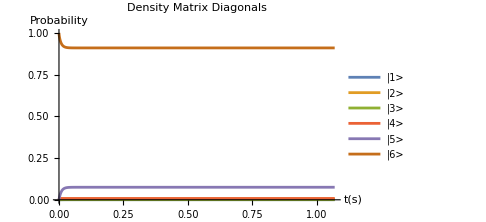

```mathematica
D1=Flatten[{Table[Subscript[ρ, i,i][t],{i,1,6}]}/.dynamicsF1];
P1=Plot[D1,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1>"],Style["|2>"],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"]},ImageSize->Medium]
```

Reverse Condition

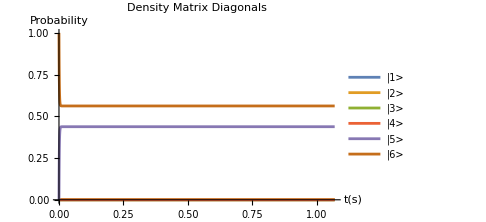

```mathematica
Flatten[{Table[Subscript[ρ, i,i][t],{i,1,6}]}/.dynamicsR1];
P1=Plot[%,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["|1>"],Style["|2>"],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"]},ImageSize->Medium]
```

#### Transition Rates

```mathematica
Subscript[Γ, P_,j_,i_]=-Subscript[ρ, i,i][t] Subscript[𝒥, P][Subscript[ω, j,i]]Subscript[n, P][Subscript[ω, j,i]]+Subscript[ρ, j,j][t]Subscript[𝒥, P][Subscript[ω, j,i]](1+Subscript[n, P][Subscript[ω, j,i]]);
```

Forward Condition

```mathematica
Flatten[{Subscript[Γ, L,1,3],Subscript[Γ, L,2,4],Subscript[Γ, L,3,5],Subscript[Γ, L,4,6],Subscript[Γ, R,1,2],Subscript[Γ, R,3,4],Subscript[Γ, R,5,6]}//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1}]/.dynamicsF1];
```

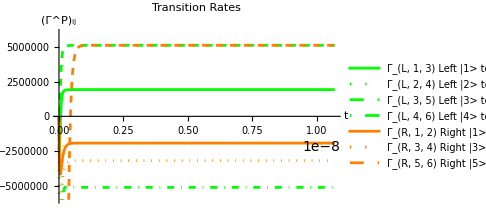

```mathematica
Plot[%,{t,0,tmax},PlotRange-> {-6×10^6,6×10^6},AxesStyle->Directive[Darker[Gray]],ImageSize->Medium,PlotLabel-> Style["Transition Rates"],AxesLabel->{"t","(Γ^P)_ij"}, PlotLegends->{
"Γ_(L, 1, 3)  Left |1> to |3>","Γ_(L, 2, 4)  Left |2> to |4>","Γ_(L, 3, 5)  Left |3> to |5>","Γ_(L, 4, 6)  Left |4> to |6>",
"Γ_(R, 1, 2)  Right |1> to |2>","Γ_(R, 3, 4)  Right |3> to |4>","Γ_(R, 5, 6)  Right |5> to |6>"},PlotStyle->{{Green},{Green,Dotted},{Green,Dashed},{Green,DotDashed},{Orange},{Orange,Dotted},{Orange,Dashed}}]
```

#### Energy Flows

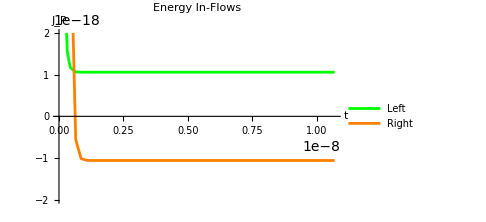

```mathematica
Flatten[{Subscript[J, L],Subscript[J, R]}//.Flatten[{Jassum1,Jassum,NBEassum,TassumF,unitassum,ωassum1,ωassum2}]/.dynamicsF1];
Plot[%,{t,0,tmax},PlotRange-> {-2×10^-18,2×10^-18},ImageSize->Medium,AxesLabel->{"t","J_P"},PlotLabel-> Style["Energy In-Flows"],PlotLegends->{"Left ","Right"},PlotStyle->{Green,Orange}]
```

#### Steady State Solutions for density matrices, transition rates and energy flows

```mathematica
varFunc[TL_,TR_,E1s_,E2s_,E3s_,gs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum1,Jassum,ωassum1,ωassum2,NBEassum,unitassum,κ->1,Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[𝔼, 1]->E1s,Subscript[𝔼, 2]->E2s,Subscript[𝔼, 3]->E3s,g->gs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^6 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]]]]];
Re[{Flatten[Table[Subscript[ρ, i,i],{i,1,6}]/.temp3],Flatten[{Subscript[Γ, L,1,3],Subscript[Γ, L,2,4],Subscript[Γ, L,3,5],Subscript[Γ, L,4,6],Subscript[Γ, R,1,2],Subscript[Γ, R,3,4],Subscript[Γ, R,5,6]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3],Flatten[{Subscript[J, L],Subscript[J, R]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3]}]]
```

```mathematica
varFunc[0.2 Tconv,0.02 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum]
varFunc[0.02 Tconv,0.2 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum]
```

{{0.000569114,0.00576966,0.000711113,0.00784533,0.0751696,0.909935},{1.92333×10^6,-1.92333×10^6,5.10857×10^6,-5.10857×10^6,-1.92333×10^6,-3.18524×10^6,5.10857×10^6},{1.05793×10^-18,-1.05793×10^-18}}

{{6.9198×10^-23,8.09599×10^-23,1.59439×10^-21,1.42161×10^-21,0.437823,0.562177},{-1.26251×10^-13,1.26251×10^-13,-1.87794×10^-11,1.87794×10^-11,1.26251×10^-13,1.86531×10^-11,3.8147×10^-6},{-3.88902×10^-36,-3.94994×10^-30}}

#### Plots for adjusting T_L and T_R (at steady state):

#### Energy Inflows

```mathematica
varEngyFunc[TL_,TR_,E1s_,E2s_,E3s_,gs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum1,Jassum,ωassum1,ωassum2,NBEassum,unitassum,κ-> 1,Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[𝔼, 1]->E1s,Subscript[𝔼, 2]->E2s,Subscript[𝔼, 3]->E3s,g->gs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^6 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]]]]];
Re[Flatten[{Subscript[J, L]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3]]]
```

```mathematica
PlotEngyFlowsWithTLTR[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
tempy1=Jconv*10^7*Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];
tempy2=Jconv*10^7*Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}],MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]}];
ListPlot[temp,AxesOrigin->{0,-0.25},AxesStyle->Directive[Darker[Gray],23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["10^-7 J_L×ℏ /Δ^2",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{{Thickness->Large,Blue},{Thickness->Large,Orange}},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],Ticks->{If[Mod[#×10,0.05×10]==0,{#,Column[{#},ItemSize->{Automatic,1.5}],{.02,0}},{#,"",{.008,.0}}]&/@Range[0,0.3,0.01],If[Mod[#,1]==0,{#,Column[{#},ItemSize->{0.8,Automatic}],{.02,0}},{#,"",{.008,.0}}]&/@{0,0.5,1,1.5,2}},ImageSize->Large]]
```

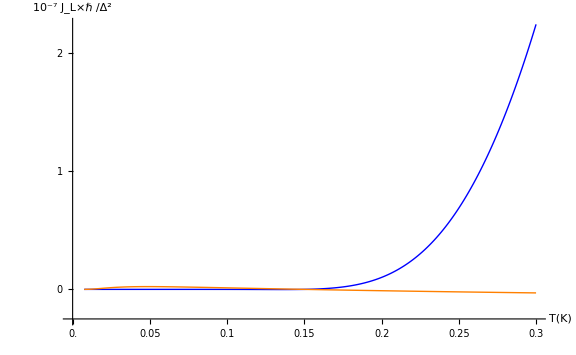

```mathematica
G1=PlotEngyFlowsWithTLTR[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,Full]
```

#### Forward and Reverse Energy Flows in Separate graphs

Forward Energy Flow

```mathematica
PlotEngyFlowsWithTLTRF[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
tempy1=10^19 Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];
(*tempy2=10^19 Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];*)
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}](*,MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]*)}];
ListPlot[temp,AxesOrigin->{0,-1},AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["J_L(10^-19J)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{{Thickness->Large,Blue}(*,{Thickness->Large,Orange}*)},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],Ticks->{If[Mod[#×10,0.05×10]==0,{#,Column[{#},ItemSize->{Automatic,1.5}],{.02,0}},{#,"",{.008,.0}}]&/@Range[0,0.3,0.01],If[Mod[#,2]==0,{#,Column[{#},ItemSize->{0.8,Automatic}],{.02,0}},{#,"",{.008,.0}}]&/@{-1,-0.5,0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}},ImageSize->Large,Epilog->{Directive[{Gray,Dashed}],Line[{{0.15,-1},{0.15,9}}]}]]
```

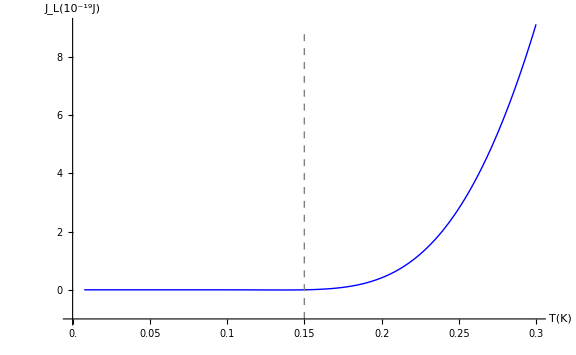

```mathematica
G1F=PlotEngyFlowsWithTLTRF[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,Full]
```

Reverse Energy Flow

```mathematica
PlotEngyFlowsWithTLTRR[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
(*tempy1=10^19 Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];*)
tempy2=10^20 Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];
temp=Table[{(*MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}],*)MapThread[List,{tempx[[;;,1]],tempy2[[;;,1]]}]}];
ListPlot[temp,(*AxesOrigin->{0,-1},*)AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["J_L(10^-20J)",23.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{(*{Thickness->Large,Blue},*){Thickness->Large,Orange}},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],Ticks->{If[Mod[#×10,0.05×10]==0,{#,Column[{#},ItemSize->{Automatic,1.5}],{.02,0}},{#,"",{.008,.0}}]&/@Range[0,0.3,0.01],If[Mod[#,2]==0,{#,Column[{#},ItemSize->{0.8,Automatic}],{.02,0}},{#,"",{.008,.0}}]&/@{-1,-0.5,0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}},ImageSize->Large,Epilog->{Directive[{Gray,Dashed}],Line[{{0.15,-3},{0.15,2}}]}]]
```

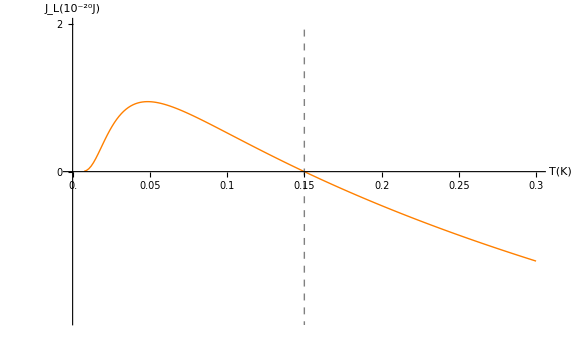

```mathematica
G1R=PlotEngyFlowsWithTLTRR[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,{{0,0.3},{-2,2}}]
```

#### Rectification Factor

```mathematica
PlotRecFacWithTL[Tmin_,Tmax_,Tres_,Tfix_,E1s_,E2s_,E3s_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp,temp1,temp2},
tempy1=10^19 Table[varEngyFunc[TL,Tfix,E1s,E2s,E3s,gs,unitassum],{TL,Tmin,Tmax,Tres}];
tempy2=10^19 Table[varEngyFunc[Tfix,TR,E1s,E2s,E3s,gs,unitassum],{TR,Tmin,Tmax,Tres}];
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
Size=Length[tempx];
temp=Table[MapThread[List,{tempx[[;;,1]],Abs[tempy1[[;;,1]]],Abs[tempy2[[;;,1]]]}]];
temp1=Table[Max[temp[[i,2]],temp[[i,3]]],{i,1,Size}];temp2=Table[MapThread[List,{tempx[[;;,1]],(Abs[(tempy1[[;;,1]]+tempy2[[;;,1]])])/temp1}]];
ListLogLinearPlot[temp2,AxesStyle->Directive[Darker[Gray],23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_L (K)",19.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["R(T_L,T_R=150mK)",21.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},Joined->True,PlotStyle->{Thickness->Large,Magenta},PlotRange->plotrange,Ticks->{Automatic,If[Mod[#×100,0.2×100]==0,{#,Column[{#},ItemSize->{1.8,Automatic}],{.02,0}},{#,"",{.008,.0}}]&/@{-0.1,-0.05,0.00,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.00,1.05,1.1}},ImageSize->700]]
```

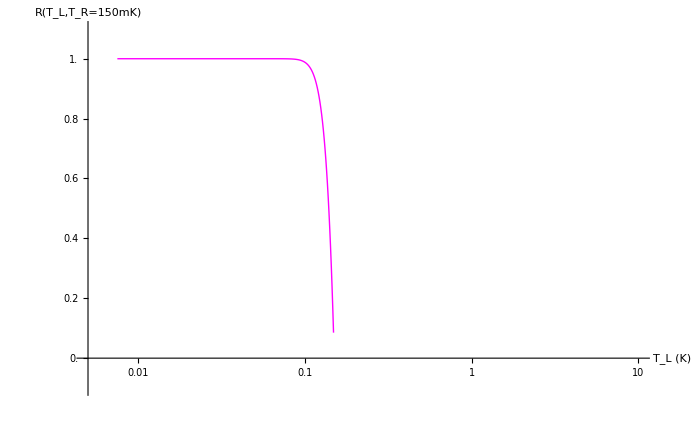

```mathematica
P1=PlotRecFacWithTL[0.005Tconv,0.1Tconv-0.001Tconv,0.001Tconv,0.1Tconv,0.95Econv,1Econv,0.05Econv,0.01Econv,{{0.005,10},{-0.1,1.1}}]
```

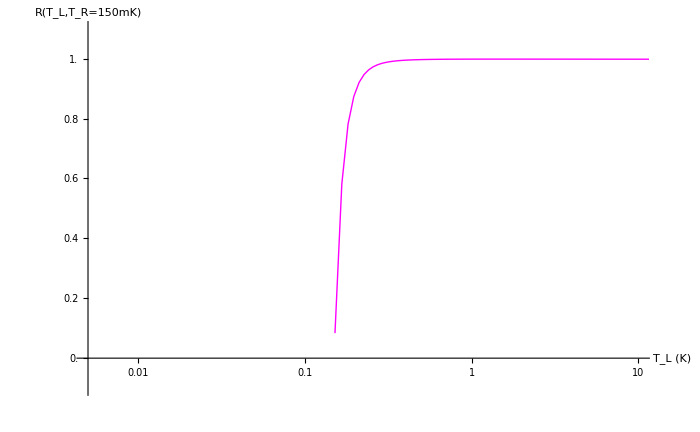

```mathematica
P2=PlotRecFacWithTL[0.1Tconv+0.001Tconv,10Tconv,0.01Tconv,0.1Tconv,0.95Econv,1Econv,0.05Econv,0.01Econv,{{0.005,10},{-0.1,1.1}}]
```

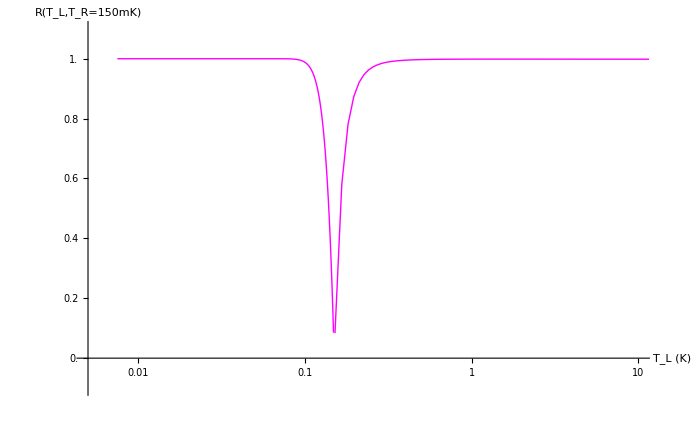

```mathematica
Show[P1,P2]
```

#### Energy Inflows change with interaction energy between qutrit and qubit

```mathematica
PlotEngyFlowsWithTLg[TLmin_,TLmax_,TLres_,TRfix_,E1s_,E2s_,E3s_,plotrange_,plotlegend_]:= 
Module[{tempx,tempy,tempz1,tempz2,temp},
tempx=Table[{TL},{TL,TLmin,TLmax,TLres}];
(*tempy=Table[{g},{g,gmin,gmax}];*)
tempz1=10^19 Table[varEngyFunc[TL,TRfix,E1s,E2s,E3s,gs,unitassum],{TL,TLmin,TLmax,TLres},{gs,{0.01Econv,0.007Econv,0.004Econv,0Econv}}];(*tempz2=10^18 Table[varEngyFunc[TRfix,TL,E1s,E2s,E3s,gs,unitassum],{TL,TLmin,TLmax,TLres},{gs,{0.04Econv,0.03Econv,0.01Econv,0Econv}}];*)temp=Table[{MapThread[List,{tempx[[;;,1]],tempz1[[;;,1]]//.{x_}:>x}],MapThread[List,{tempx[[;;,1]],tempz1[[;;,2]]//.{x_}:>x}],MapThread[List,{tempx[[;;,1]],tempz1[[;;,3]]//.{x_}:>x}],MapThread[List,{tempx[[;;,1]],tempz1[[;;,4]]//.{x_}:>x}]}];
ListPlot[temp,AxesOrigin->{0,-1},AxesStyle->Directive[Black,26.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_L(K)",26.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["J_L(10^-19J)",26.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},PlotStyle->{{Thickness->Large,Orange},{Thickness->Large,Blue},{Thickness->Large,Green},{Thickness->Large,Red}},(*PlotLegends->Placed[plotlegend,{Center,Below}],LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->26.5],*)PlotRange->plotrange,Ticks->{If[Mod[#×100,0.05×100]==0,{#,Column[{#},ItemSize->{Automatic,1.5}],{.02,0}},{#,"",{.008,.0}}]&/@Range[0,0.3,0.01],If[Mod[#,5]==0,{#,Column[{#},ItemSize->{1.3,Automatic}],{.02,0}},{#,"",{.008,.0}}]&/@{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}},ImageSize->Large,Joined->True]]
```

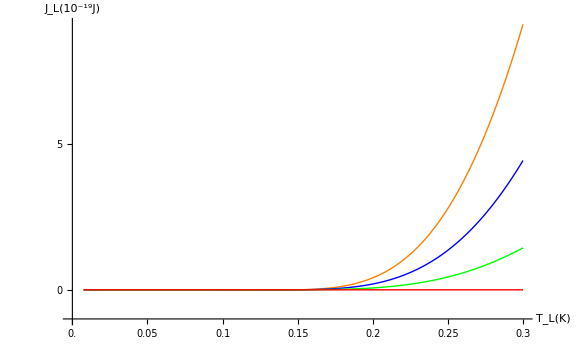

```mathematica
PlotEngyFlowsWithTLg[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,Full,{"T_L=T, T_R=150mK, g=0.01E","T_L=T, T_R=150mK, g=0.007E","T_L=T, T_R=150mK, g=0.004E","T_L=T, T_R=150mK, g=0"}]
```

```mathematica
PlotReverseEngyFlowsWithTLg[TLmin_,TLmax_,TLres_,TRfix_,E1s_,E2s_,E3s_,plotrange_,plotlegend_]:= 
Module[{tempx,tempy,tempz1,tempz2,temp},
tempx=Table[{TL},{TL,TLmin,TLmax,TLres}];
tempz2=10^20 Table[varEngyFunc[TRfix,TL,E1s,E2s,E3s,gs,unitassum],{TL,TLmin,TLmax,TLres},{gs,{0.01Econv,0.007Econv,0.004Econv,0Econv}}];
temp=Table[{MapThread[List,{tempx[[;;,1]],tempz2[[;;,1]]//.{x_}:>x}],MapThread[List,{tempx[[;;,1]],tempz2[[;;,2]]//.{x_}:>x}],MapThread[List,{tempx[[;;,1]],tempz2[[;;,3]]//.{x_}:>x}],MapThread[List,{tempx[[;;,1]],tempz2[[;;,4]]//.{x_}:>x}]}];
ListPlot[temp,AxesOrigin->{0,-0.5},AxesStyle->Directive[Black,26.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T(K)",26.5,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["J_L(10^-20J)",26.5,FontFamily->"Times New Roman",SingleLetterItalics->False]},PlotStyle->{{Thickness->Large,Orange},{Thickness->Large,Blue},{Thickness->Large,Green},{Thickness->Large,Red}},PlotRange->plotrange,ImageSize->Large,Joined->True]]
```

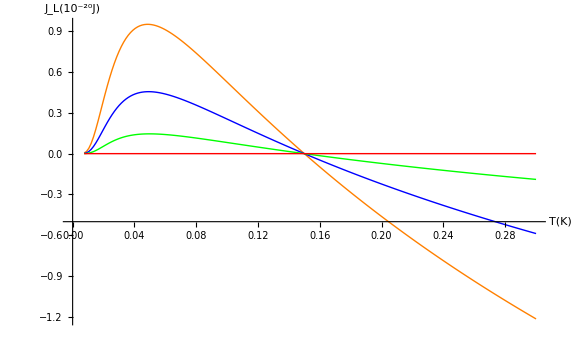

```mathematica
PlotReverseEngyFlowsWithTLg[0.005Tconv,0.20Tconv,0.001Tconv,0.1Tconv,0.95 Econv,1Econv,0.05Econv,Full,{"T_L=150mK, T_R=T, g=0.01E","T_L=150mK, T_R=T, g=0.007E","T_L=150mK, T_R=T, g=0.004E","T_L=150mK, T_R=T, g=0"}]
```

#### State and transition rate diagrams:

#### Forward Biased Diode

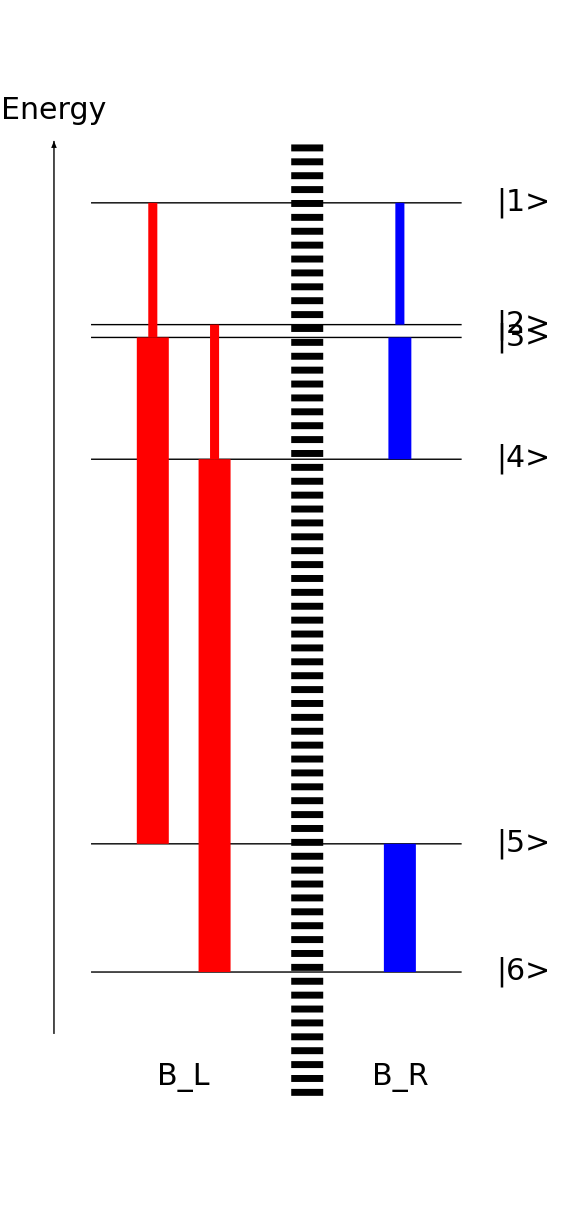

```mathematica
TassumF={Subscript[T, L]-> 0.2 Tconv,Subscript[T, R]-> 0.02 Tconv,Subscript[𝔼, 1]->0.8Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.2 Econv,g->0.01Econv,κ-> 1 };
Evals={HsEVal}//.Flatten[{unitassum,TassumF}];
ypoints=Table[50×10^23×Evals[[1,1]][[y]],{y,1,6}];
States=Table[{"|1>","|2>","|3>","|4>","|5>","|6>"}];
SState=varFunc[0.2 Tconv,0.1 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum];
MaxRate=0.5*Max[SState[[2]]];
Graphics[{
Table[Line[{{15,50×10^23×Evals[[1,1]][[y]]},{75,ypoints[[y]]}}],{y,1,6}],
Table[Text[Style[States[[i]],30,FontFamily->"Times New Roman"],{85,50×10^23×Evals[[1,1]][[i]]}],{i,1,6}],Arrowheads[0.07],
Arrow[{{9,50×10^23×Evals[[1,1]][[6]]-10},{9,50×10^23×Evals[[1,1]][[1]]+10}}],
Text[Style["Energy",30,FontFamily->"Times New Roman"],{9,52×10^23×Evals[[1,1]][[1]]+10}],
Text[Style["B_L",30,FontFamily->"Times New Roman"],{30,50×10^23×Evals[[1,1]][[6]]-17}],Text[Style["B_R",30,FontFamily->"Times New Roman"],{65,50×10^23×Evals[[1,1]][[6]]-17}],
Red,Arrowheads[0.1],Thickness[0.02*Abs[SState[[2]][[1]]]/MaxRate],If[SState[[2]][[1]]>0,Arrow[{{25,ypoints[[1]]},{25,ypoints[[3]]}}],Arrow[{{25,ypoints[[3]]},{25,ypoints[[1]]}}]],
Red,Arrowheads[0.1],Thickness[0.02*Abs[SState[[2]][[2]]]/MaxRate],If[SState[[2]][[2]]>0,Arrow[{{35,ypoints[[2]]},{35,ypoints[[4]]}}],Arrow[{{35,ypoints[[4]]},{35,ypoints[[2]]}}]],
Red,Arrowheads[0.12],Thickness[0.02*Abs[SState[[2]][[3]]]/MaxRate],If[SState[[2]][[3]]>0,Arrow[{{25,ypoints[[3]]},{25,ypoints[[5]]}}],Arrow[{{25,ypoints[[5]]},{25,ypoints[[3]]}}]],
Red,Arrowheads[0.12],Thickness[0.02*Abs[SState[[2]][[4]]]/MaxRate],If[SState[[2]][[4]]>0,Arrow[{{35,ypoints[[4]]},{35,ypoints[[6]]}}],Arrow[{{35,ypoints[[6]]},{35,ypoints[[4]]}}]],
Blue,Arrowheads[0.06],Thickness[0.02*Abs[SState[[2]][[5]]]/MaxRate],If[SState[[2]][[5]]>0,Arrow[{{65,ypoints[[1]]},{65,ypoints[[2]]}}],Arrow[{{65,ypoints[[2]]},{65,ypoints[[1]]}}]],
Blue,Arrowheads[0.09],Thickness[0.02*Abs[SState[[2]][[6]]]/MaxRate],If[SState[[2]][[6]]>0,Arrow[{{65,ypoints[[3]]},{65,ypoints[[4]]}}],Arrow[{{65,ypoints[[4]]},{65,ypoints[[3]]}}]],
Blue,Arrowheads[0.12],Thickness[0.02*Abs[SState[[2]][[7]]]/MaxRate],If[SState[[2]][[7]]>0,Arrow[{{65,ypoints[[5]]},{65,ypoints[[6]]}}],Arrow[{{65,ypoints[[6]]},{65,ypoints[[5]]}}]],
Thickness[Tiny],Black,Dashed,Line[{{50,50×10^23×Evals[[1,1]][[6]]-20},{50,50×10^23×Evals[[1,1]][[1]]+10}}]
},ImageSize->Large]
```

#### Reverse Biased Diode

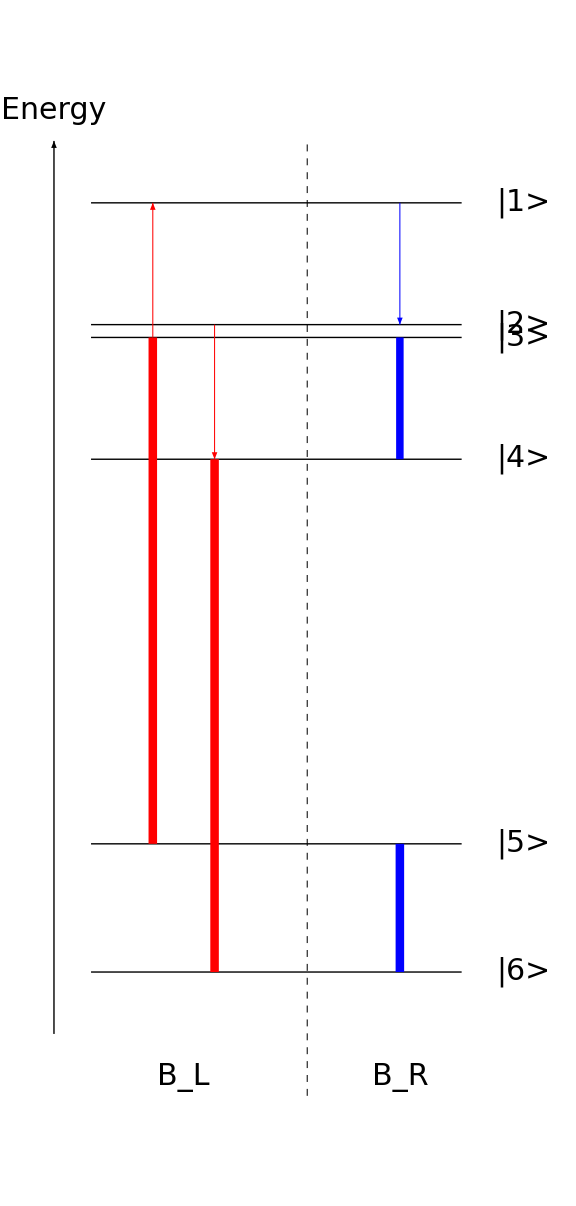

```mathematica
TassumF={Subscript[T, L]-> 0.2 Tconv,Subscript[T, R]-> 0.02 Tconv,Subscript[𝔼, 1]->0.8Econv,Subscript[𝔼, 2]->1 Econv,Subscript[𝔼, 3]->0.2 Econv,g->0.01Econv,κ-> 1 };
Evals={HsEVal}//.Flatten[{unitassum,TassumF}];
ypoints=Table[50×10^23×Evals[[1,1]][[y]],{y,1,6}];
States=Table[{"|1>","|2>","|3>","|4>","|5>","|6>"}];
SState=varFunc[0.1 Tconv,0.2 Tconv,0.95 Econv,1Econv,0.05Econv,0.01 Econv,unitassum];
Graphics[{
Table[Line[{{15,50×10^23×Evals[[1,1]][[y]]},{75,ypoints[[y]]}}],{y,1,6}],
Table[Text[Style[States[[i]],30,FontFamily->"Times New Roman"],{85,50×10^23×Evals[[1,1]][[i]]}],{i,1,6}],Arrowheads[0.07],
Arrow[{{9,50×10^23×Evals[[1,1]][[6]]-10},{9,50×10^23×Evals[[1,1]][[1]]+10}}],Text[Style["Energy",30,FontFamily->"Times New Roman"],{9,52×10^23×Evals[[1,1]][[1]]+10}],
Text[Style["B_L",30,FontFamily->"Times New Roman"],{30,50×10^23×Evals[[1,1]][[6]]-17}],Text[Style["B_R",30,FontFamily->"Times New Roman"],{65,50×10^23×Evals[[1,1]][[6]]-17}],
Red,Arrowheads[0.07],Thickness[0.4*Abs[SState[[2]][[1]]]/MaxRate],If[SState[[2]][[1]]>0,Arrow[{{25,ypoints[[1]]},{25,ypoints[[3]]}}],Arrow[{{25,ypoints[[3]]},{25,ypoints[[1]]}}]],
Red,Thickness[0.4*Abs[SState[[2]][[2]]]/MaxRate],If[SState[[2]][[2]]>0,Arrow[{{35,ypoints[[2]]},{35,ypoints[[4]]}}],Arrow[{{35,ypoints[[4]]},{35,ypoints[[2]]}}]],
Red,Thickness[0.4*Abs[SState[[2]][[3]]]/MaxRate],If[SState[[2]][[3]]>0,Arrow[{{25,ypoints[[3]]},{25,ypoints[[5]]}}],Arrow[{{25,ypoints[[5]]},{25,ypoints[[3]]}}]],
Red,Thickness[0.4*Abs[SState[[2]][[4]]]/MaxRate],If[SState[[2]][[4]]>0,Arrow[{{35,ypoints[[4]]},{35,ypoints[[6]]}}],Arrow[{{35,ypoints[[6]]},{35,ypoints[[4]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[5]]]/MaxRate],If[SState[[2]][[5]]>0,Arrow[{{65,ypoints[[1]]},{65,ypoints[[2]]}}],Arrow[{{65,ypoints[[2]]},{65,ypoints[[1]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[6]]]/MaxRate],If[SState[[2]][[6]]>0,Arrow[{{65,ypoints[[3]]},{65,ypoints[[4]]}}],Arrow[{{65,ypoints[[4]]},{65,ypoints[[3]]}}]],
Blue,Thickness[0.4*Abs[SState[[2]][[7]]]/MaxRate],If[SState[[2]][[7]]>0,Arrow[{{65,ypoints[[5]]},{65,ypoints[[6]]}}],Arrow[{{65,ypoints[[6]]},{65,ypoints[[5]]}}]],
Thickness[Tiny],Black,Dashed,Line[{{50,50×10^23×Evals[[1,1]][[6]]-20},{50,50×10^23×Evals[[1,1]][[1]]+10}}]
},ImageSize->Large]
```